### Parameter values

```mathematica
τk=100;
τna=20;
γ=10;
Nai0=10;
Kbath=8.5;
Ko0=3;
Capa=40;
gL=4;
νmax=100;
kv=20;
Vth=25;
Gsyn=5*gL;
δk=0.02;
δna=0.03;
ρ=0.2;
τxD=2;
δxD=0.01;
noiseStrength=30;
```

### Na-K pump current

```mathematica
Ipump[ρ_,Ko_,Nai_]:=ρ/((1+Exp[3.5-Ko])(1+Exp[(25-Nai)/3]))
Plot3D[Ipump[ρ,Ko,Nai],{Ko,0,15},{Nai,0,35}]
```

-Graphics3D-

### Frequency vs depolarization

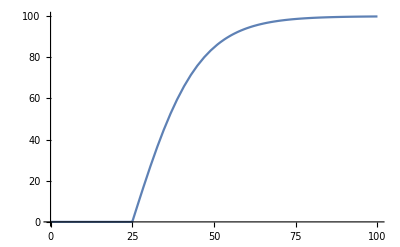

```mathematica
Clear[ν];
ν[v_]:=If[v≤Vth,0,νmax*(2/(1+Exp[(-2*(v-Vth))/kv])-1)];
Plot[ν[V],{V,0,100}]
```

### Potassium current

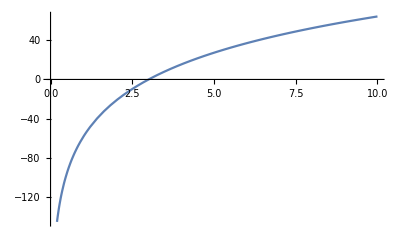

```mathematica
Plot[gL/2*(26.6*Log[k/130]-26.6*Log[Ko0/130]),{k,0,10}]
```

## Complete system without noise

```mathematica
Eq1=D[Ko[t],t]==(Kbath-Ko[t])/τk-2 γ Ipump[ρ,Ko[t],Nai[t]]+δk ν[V[t]];
Eq2=D[Nai[t],t]==(Nai0-Nai[t])/τna-3 Ipump[ρ,Ko[t],Nai[t]]+δna ν[V[t]];
Eq3=(Capa*D[V[t],t])/1000==-gL*V[t]+gL/2*(26.6*Log[Ko[t]/130]-26.6*Log[Ko0/130])+Gsyn*ν[V[t]]*(xD[t]-0.5);
Eq4=D[xD[t],t]==(1-xD[t])/τxD-δxD*ν[V[t]]*xD[t];
IC1=Ko[0]==Ko0;
IC2=Nai[0]==Nai0;
IC3=V[0]==0;
IC4=xD[0]==1;
```

```mathematica
sol=NDSolve[{Eq1,Eq2,Eq3,Eq4,IC1,IC2,IC3,IC4},{Ko,Nai,V,xD},{t,0,1000}]
```

{{Ko→InterpolatingFunction[{{0., 1000.}}, <>],Nai→InterpolatingFunction[{{0., 1000.}}, <>],V→InterpolatingFunction[{{0., 1000.}}, <>],xD→InterpolatingFunction[{{0., 1000.}}, <>]}}

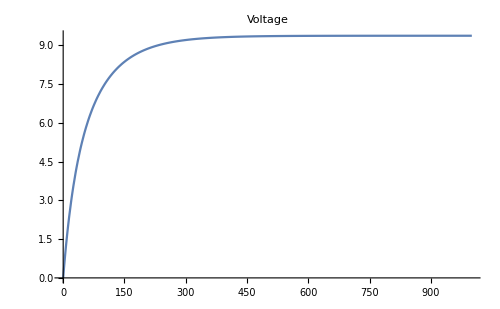
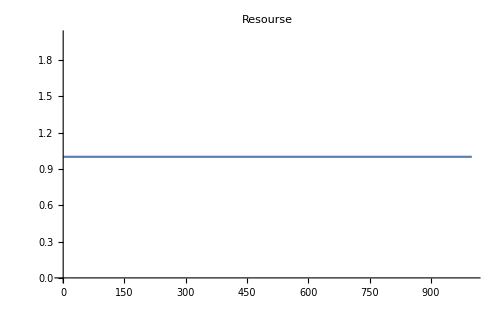
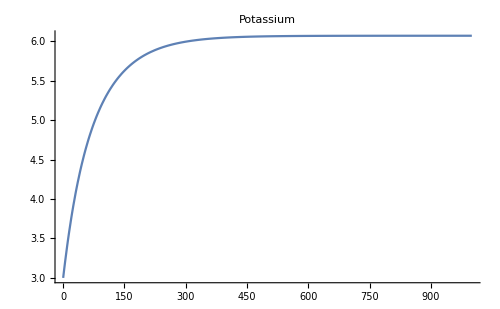
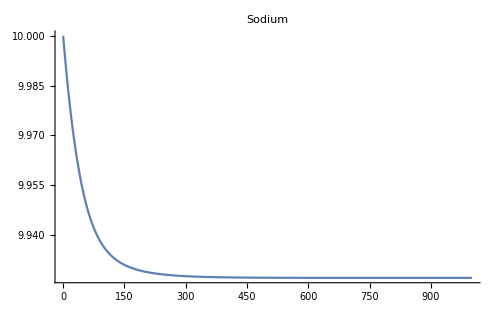
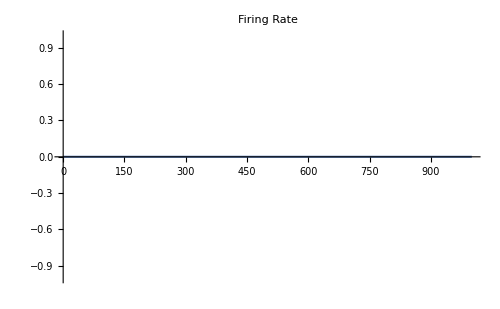
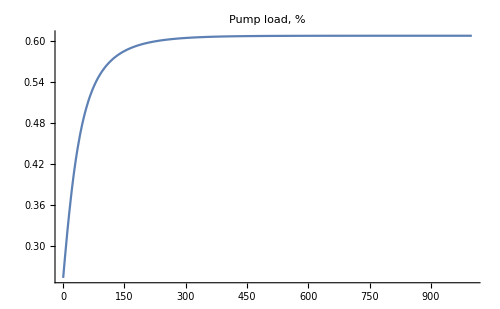

```mathematica
Column[{
Row[{Plot[(V/.sol[[1]])[t],{t,0,1000},PlotLabel->"Voltage",ImageSize->500,PlotRange->Full],Plot[(xD/.sol[[1]])[t],{t,0,1000},PlotLabel->"Resourse",ImageSize->500,PlotRange->Full]}],
Row[{Plot[(Ko/.sol[[1]])[t],{t,0,1000},PlotLabel->"Potassium",ImageSize->500,PlotRange->Full],Plot[(Nai/.sol[[1]])[t],{t,0,1000},PlotLabel->"Sodium",ImageSize->500,PlotRange->Full]}],
Row[{Plot[ν[(V/.sol[[1]])[t]],{t,0,1000},PlotLabel->"Firing Rate",ImageSize->500,PlotRange->Full],
Plot[(Ipump[100,Ko[t],Nai[t]]/.sol[[1]]),{t,0,1000},PlotLabel->"Pump load, %",ImageSize->500,PlotRange->Full]}]
}]
```

## Complete system with noise

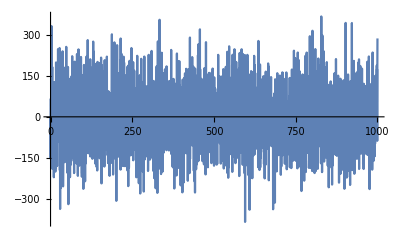

```mathematica
Clear[noiseFunction];noiseFreq=1000;
noiseFunction[t_]=Interpolation[
Partition[
Riffle[
Range[0,1000,1/noiseFreq],
Prepend[RandomVariate[NormalDistribution[0,noiseStrength*gL],1000*noiseFreq],0]
],
2]
,Method->"Hermite"][t];
Plot[noiseFunction[t],{t,0,1000}]
```

```mathematica
Eq12=D[Ko[t],t]==(Kbath-Ko[t])/τk-2 γ Ipump[ρ,Ko[t],Nai[t]]+δk ν[V[t]];
Eq22=D[Nai[t],t]==(Nai0-Nai[t])/τna-3 Ipump[ρ,Ko[t],Nai[t]]+δna ν[V[t]];
Eq32=Capa/1000*D[V[t],t]==-gL*V[t]+gL/2*(26.6*Log[Ko[t]/130]-26.6*Log[Ko0/130])+Gsyn*ν[V[t]]*(xD[t]-0.5)+noiseFunction[t];
Eq42=D[xD[t],t]==(1-xD[t])/τxD-xD[t]*δxD*ν[V[t]];
IC12=Ko[0]==Ko0;
IC22=Nai[0]==Nai0;
IC32=V[0]==0;
IC42=xD[0]==1;
```

```mathematica
sol2=Quiet@NDSolve[{Eq12,Eq22,Eq32,Eq42,IC12,IC22,IC32,IC42},{Ko,Nai,V,xD},{t,0,1000},MaxSteps->100000000]
```

{{Ko→InterpolatingFunction[{{0., 1000.}}, <>],Nai→InterpolatingFunction[{{0., 1000.}}, <>],V→InterpolatingFunction[{{0., 1000.}}, <>],xD→InterpolatingFunction[{{0., 1000.}}, <>]}}

```mathematica
Clear[Voltage,Resourse,Potassium,Sodium];
Voltage[t_]=V[t]/.sol2[[1]];
Resourse[t_]=xD[t]/.sol2[[1]];
Potassium[t_]=Ko[t]/.sol2[[1]];
Sodium[t_]=Nai[t]/.sol2[[1]];
```

```mathematica
FreqTable=Table[{t,ν[Voltage[t]]},{t,0,1000,0.001}];
LoadTable=Table[{t,Ipump[100,Potassium[t],Sodium[t]]},{t,0,1000,0.001}];
VoltageTable=Table[{t,Voltage[t]},{t,0,1000,0.001}];
ResourseTable=Table[{t,100*Resourse[t]},{t,0,1000,0.001}];
SodiumTable=Table[{t,Sodium[t]},{t,0,1000,0.001}];
PotassiumTable=Table[{t,Potassium[t]},{t,0,1000,0.001}];
```

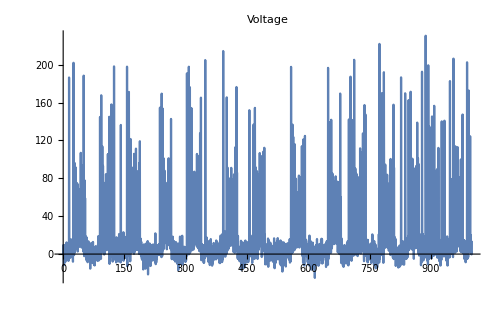
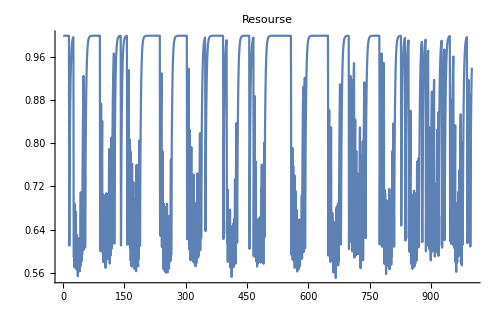
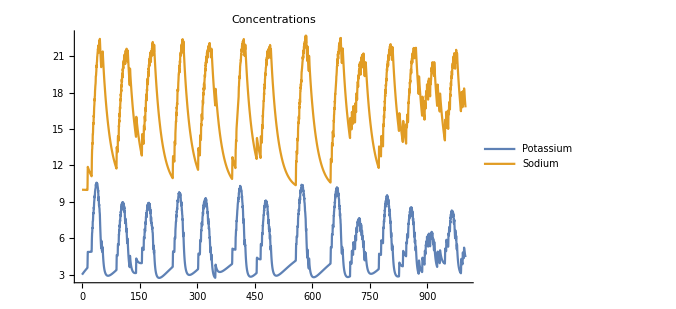
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-

```mathematica
Column[{
Row[{
Plot[Voltage[t],{t,0,1000},PlotLabel->"Voltage",ImageSize->500,PlotRange->Full],Plot[Resourse[t],{t,0,1000},PlotLabel->"Resourse",ImageSize->500,PlotRange->Full]
}],
Row[{
Plot[{Potassium[t],Sodium[t]},{t,0,1000},PlotLabel->"Concentrations",ImageSize->500,PlotRange->Full,PlotLegends->{"Potassium","Sodium"}]
}],
Row[{
ListPlot[FreqTable,PlotLabel->"Firing Rate",ImageSize->500,PlotRange->Full,Joined->True],
ListPlot[LoadTable,PlotLabel->"Pump load, %",ImageSize->500,PlotRange->Full,Joined->True]
}]
}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Quiet@DeleteFile["voltage - 1000.bin32ad"];
Quiet@DeleteFile["synres - 1000.bin32ad"];
Quiet@DeleteFile["sodium - 1000.bin32ad"];
Quiet@DeleteFile["potassium - 1000.bin32ad"];
Quiet@DeleteFile["frate - 1000.bin32ad"];
Quiet@DeleteFile["pumpload - 1000.bin32ad"];
BinaryWrite["voltage - 1000.bin32ad",VoltageTable[[All,2]],"Real32"];
Close["voltage - 1000.bin32ad"];
BinaryWrite["synres - 1000.bin32ad",ResourseTable[[All,2]],"Real32"];
Close["synres - 1000.bin32ad"];
BinaryWrite["potassium - 1000.bin32ad",PotassiumTable[[All,2]],"Real32"];
Close["potassium - 1000.bin32ad"];
BinaryWrite["sodium - 1000.bin32ad",SodiumTable[[All,2]],"Real32"];
Close["sodium - 1000.bin32ad"];
BinaryWrite["frate - 1000.bin32ad",FreqTable[[All,2]],"Real32"];
Close["frate - 1000.bin32ad"];
BinaryWrite["pumpload - 1000.bin32ad",LoadTable[[All,2]],"Real32"];
Close["pumpload - 1000.bin32ad"];
```